Part 1 -- Tossing Coins:

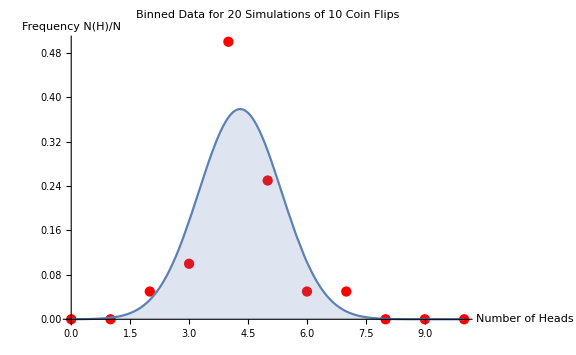

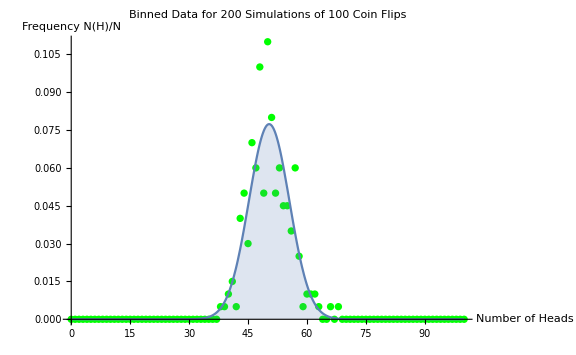

Part 2 -- Random Walk in 1D:

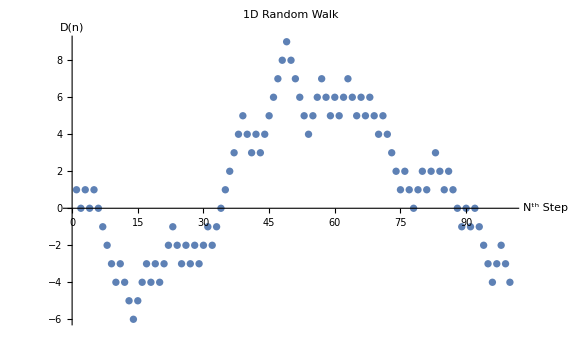

Extra Credit -- Random walk in 2D:

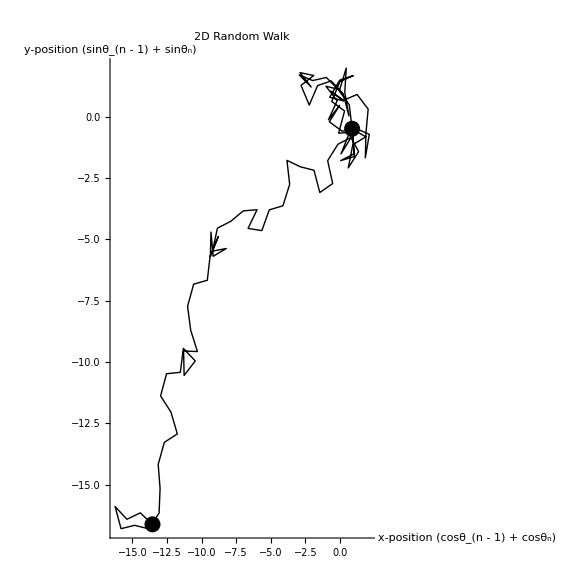

```mathematica
(*Probability-M3*)
(*Jared Frazier*)
(*Description:

Simulate probabilistic outcomes and frequencies of simulated coin tosses as well as random walk in one and two
dimensions.

Oddly, for the second run where the number of simulations and number of coin tosses increases, the frequency
of heads releative to the number of tosses for a given simulation declines. In the first figure, the frequency
appears to be the expected 0.50 for heads-tails coin tosses, while for the second simulation it appears to be
~0.15.

*)
(*Due: 09-28-2020*)

Clear["Global`"]

(**************************************************************************)
                        (*Part 1 -- Tossing Coins*)
(**************************************************************************)
Print["Part 1 -- Tossing Coins:"]

(*Set seed to get consistent random results for testing*)
SeedRandom[12345] 

(*Function with no params --> 1 = heads, 0 = tails*)
coinFlip := RandomChoice[{1,0}]; 

(*Number of time to flip coin*)
n = 10; 

(*20 total simulations*)
simTotal = 2*n; 

(*Track number of simulations where Table[] = {{headCount,tailcount}....}*)
simulationTable20 = Table[0,simTotal,2]; (*20x2 table w/ all eles @ 0*)

(*Simulation loop*)
For[i = 1, i ≤ simTotal, i++,(*Simulate simTotal time where simTotal = 20 or 2n*)
    For[j = 1, j <= n, j++,  (*Flip coin n times where n = 10*)
       If[coinFlip == 1, 
            simulationTable20[[i,1]]++, 
            simulationTable20[[i,2]]++
       ]
    ]
]

(*Bin Table*)
binTable = Table[0,n+1,2]; (*11x2 rows *)
For[i = 0, i <= n, i++,    (*Initialize 1st column of bin table*)
    binTable[[i+1,1]] = i
]

(*Iterate through Simulation Table and increment appropriate frequency in binTable*)
For[i = 1, i ≤ simTotal, i++,(*Simulate simTotal time where simTotal = 20 or 2n*)
    For[j = 1, j ≤ n+1, j++,
       If[simulationTable20[[i,1]] == binTable[[j,1]],
          binTable[[j,2]]++
       ]
    ]
]

(*Sum of frequencies for binTable*)
sumFrequencies = 0;
For[i = 1, i ≤n+1, i++,
    sumFrequencies += binTable[[i,2]]
]

(*Convert table to P(H) for normal distribution*)
For[i = 1, i ≤ n+1, i++,
    binTable[[i,2]] = binTable[[i,2]]/sumFrequencies
]

(*Calculating mean, and standard deviation of frequency distribution table binTable*)
meanNumerator = 0;
meanDenominator = 1; (*Sum of P(H) must be 1*)
For[i = 1, i ≤ n+1, i++,
    meanNumerator += binTable[[i,1]]*binTable[[i,2]]
]
meanBinTable = meanNumerator/meanDenominator; (*xbar = (Σ(xf))/Σf =(mean numerator)/(mean denominator)*)
varianceNumerator = 0;
For[i = 1, i ≤ n+1, i++,
    varianceNumerator += binTable[[i,2]]*(binTable[[i,1]]-meanBinTable)^2 
]
varianceBinTable = varianceNumerator/1;
stdDevBinTable = Sqrt[varianceBinTable];

(*Plot data values*)
Show[
    ListPlot[binTable, PlotStyle->Red, 
    PlotLabel->"Binned Data for 20 Simulations of 10 Coin Flips",
    AxesLabel->{"Number of Heads","Frequency N(H)/N"}, ImageSize->Large
    ],
    Plot[PDF[NormalDistribution[meanBinTable,stdDevBinTable], x], {x,0,n},
    Filling->Axis
    ]
]
(****************************************************************************)
                          (*Part 1 -- CTD N=100*)
(*Do binned data for N=100 flips therefore simTotal = 100*2 = 200 simulations*)
(****************************************************************************)

n2 = 100; (*Number of time to flip coin*)
simTotal2 = 2*n2; (*20 total simulations*)
(*Track number of simulations where Table[] = {{headCount,tailcount}....}*)
simulationTable200 = Table[0,simTotal2,2]; (*200x2 table w/ all eles @ 0*)

(*Simulation loop*)
For[i = 1, i ≤ simTotal2, i++,(*Simulate simTotal time where simTotal = 200 or 2n*)
    For[j = 1, j <= n2, j++,  (*Flip coin n times where n = 10*)
       If[coinFlip == 1, 
            simulationTable200[[i,1]]++, 
            simulationTable200[[i,2]]++
       ]
    ]
]

(*Bin Table*)
binTable2 = Table[0,n2+1,2];
For[i = 0, i ≤ n2, i++, (*Initialize 1st column of bin table*)
    binTable2[[i+1,1]] = i
]

(*Iterate through Simulation Table and increment appropriate frequency in binTable*)
For[i = 1, i ≤ simTotal2, i++,
    For[j = 1, j ≤ n2+1, j++,
       If[simulationTable200[[i,1]] == binTable2[[j,1]],
          binTable2[[j,2]]++
       ]
    ]
]

(*Sum of frequencies for binTable2*)
sumFrequencies2 = 0;
For[i = 1, i ≤n2+1, i++,
    sumFrequencies2 += binTable2[[i,2]]
]

(*Convert binTable frequency (whole num) to fraction of total simulations, or P(H)*)
For[i = 1, i ≤ n2+1, i++,
    binTable2[[i,2]] = binTable2[[i,2]]/sumFrequencies2
]

(*Calculating mean, and standard deviation of frequency distribution table binTable*)
meanNumerator2 = 0;
meanDenominator2 = 1; (*Sum P(H) must be 1*)
For[i = 1, i ≤ n2+1, i++,
    meanNumerator2 += binTable2[[i,1]]*binTable2[[i,2]]
]
meanBinTable2 = meanNumerator2/meanDenominator2; (*xbar = (Σ(xf))/Σf*)
varianceNumerator2 = 0;
For[i = 1, i ≤ n2+1, i++,
    varianceNumerator2 += binTable2[[i,2]]*(binTable2[[i,1]]-meanBinTable2)^2 
]
varianceBinTable2 = varianceNumerator2/1;
stdDevBinTable2 = Sqrt[varianceBinTable2];

(*Plot data*)
Show[
    ListPlot[binTable2, PlotStyle->Green, 
    PlotLabel->"Binned Data for 200 Simulations of 100 Coin Flips",
    AxesLabel->{"Number of Heads","Frequency N(H)/N"}, ImageSize->Large, PlotRange->Full
    ],
    Plot[PDF[NormalDistribution[meanBinTable2, stdDevBinTable2],x], {x,0,n2},
    Filling->Axis, PlotRange->Full
    ]
]
(**************************************************************************)
                        (*Part 2 -- Random Walk*)
(**************************************************************************)

Print["Part 2 -- Random Walk in 1D:"]

(*0 indicates left step -1, 1 indicates right step*)
randomWalk1D := RandomChoice[{0,1}]

(*Build yList, which is dn or distance from origin, with "recurisve" style function*)
dn = {}; (*empty list*)
If[randomWalk1D == 1, (*Initialize first step N = 1 of dn list*)
   AppendTo[dn,1];,
   AppendTo[dn,-1];
]

(*Random walk through N=100*)
nSteps = 100;
For[i=2, i ≤ nSteps, i++,
    If[randomWalk1D == 1,
       AppendTo[dn, dn[[i-1]] + 1],
       AppendTo[dn, dn[[i-1]] - 1]
    ]
]

(*Build table of X = N steps and Y = distance from origin*)
dnVsN = Table[0,100,2];
For[i=1, i <= nSteps, i++,
    dnVsN[[i,1]] = i;
    dnVsN[[i,2]] = dn[[i]];
]

(*Plot random walk*)
ListPlot[dnVsN, PlotLabel->"1D Random Walk", AxesLabel->{"N^th Step","D(n)"}]

(**************************************************************************)
                     (*Extra Credit -- Random Walk in 2D*)
(**************************************************************************)

(*Random walk in 2D through plane*)
randomTheta := RandomReal[{0,2*Pi}] (*Random phase angle*)
randomWalk2DTable = Table[0,100,2]; (*Table of values X = CosTheta Y = SinTheta, unit vector means r = 1*)
initTheta = randomTheta; (*Initial random phase angle*)
randomWalk2DTable[[1,1]] = Cos[initTheta]; (*Initial x coordinate*)
randomWalk2DTable[[1,2]] = Sin[initTheta]; (*Initial y coordinate*)
For[i = 2, i ≤ nSteps, i++,                (*Take 99 additional random steps*)
    theta = randomTheta;                   (*Random phase angle for next move*)
    randomWalk2DTable[[i,1]] = randomWalk2DTable[[i-1,1]] + Cos[theta];  (*Increment previous x position*)
    randomWalk2DTable[[i,2]] = randomWalk2DTable[[i-1,2]] + Sin[theta];  (*Increment previous y position*)
]

(*Plot random walk*)
Print["Extra Credit -- Random walk in 2D:"]
Show[
    Graphics[{Line[randomWalk2DTable],{PointSize[.02],Point[randomWalk2DTable[[{1,-1}]]]}}, Axes->True], AspectRatio->Automatic,
    PlotLabel->"2D Random Walk", AxesLabel->{"x-position (cosθ_(n - 1) + cosθ_n)", "y-position (sinθ_(n - 1) + sinθ_n)"}
]
```